```mathematica
WE={D[u[x,t],{t,2}]-4( D[u[x,t],{x,2}])==0}
```

{u^(0,2)[x,t]-4 u^(2,0)[x,t]==0}

```mathematica
bc={u[0,t]==0,u[1,t]==0};
```

```mathematica
ic={u[x,0]==Sin[π x],u[x,1]==Sin[π x]}
```

{u[x,0]==Sin[π x],u[x,1]==Sin[π x]}

```mathematica
usol=First[u/.NDSolve[Flatten[{WE,bc,ic}],u,{x,0,1},{t,0,1}]]
```

InterpolatingFunction[…]

```mathematica
HeatMap
```

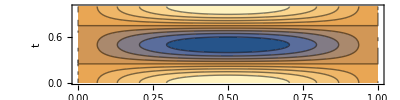

```mathematica
ContourPlot[usol[x,t],{x,0,1},{t,0,1},BaseStyle->FontSize->22,FrameLabel->{"x","t"},PlotLegends->Automatic,LabelStyle->FontSize->18,AspectRatio->1/4]
```

```mathematica
Length[Table[i,{i,0,1,1/10}]]
```

11

```mathematica
linsp10={0.,0.11111111,0.22222222,0.33333333,0.44444444,0.55555556,0.66666667,0.77777778,0.88888889,1.}
```

{0.,0.111111,0.222222,0.333333,0.444444,0.555556,0.666667,0.777778,0.888889,1.}

```mathematica
linsp15={0.,0.07142857,0.14285714,0.21428571,0.28571429,0.35714286,0.42857143,0.5,0.57142857,0.64285714,0.71428571,0.78571429,0.85714286,0.92857143,1.}
```

{0.,0.0714286,0.142857,0.214286,0.285714,0.357143,0.428571,0.5,0.571429,0.642857,0.714286,0.785714,0.857143,0.928571,1.}

```mathematica
linsp20={0.,0.05263158,0.10526316,0.15789474,0.21052632,0.26315789,0.31578947,0.36842105,0.42105263,0.47368421,0.52631579,0.57894737,0.63157895,0.68421053,0.73684211,0.78947368,0.84210526,0.89473684,0.94736842,1.}
```

{0.,0.0526316,0.105263,0.157895,0.210526,0.263158,0.315789,0.368421,0.421053,0.473684,0.526316,0.578947,0.631579,0.684211,0.736842,0.789474,0.842105,0.894737,0.947368,1.}

```mathematica
linsp25={0.,0.04166667,0.08333333,0.125,0.16666667,0.20833333,0.25,0.29166667,0.33333333,0.375,0.41666667,0.45833333,0.5,0.54166667,0.58333333,0.625,0.66666667,0.70833333,0.75,0.79166667,0.83333333,0.875,0.91666667,0.95833333,1.}
```

{0.,0.0416667,0.0833333,0.125,0.166667,0.208333,0.25,0.291667,0.333333,0.375,0.416667,0.458333,0.5,0.541667,0.583333,0.625,0.666667,0.708333,0.75,0.791667,0.833333,0.875,0.916667,0.958333,1.}

```mathematica
linsp30={0.,0.03448276,0.06896552,0.10344828,0.13793103,0.17241379,0.20689655,0.24137931,0.27586207,0.31034483,0.34482759,0.37931034,0.4137931,0.44827586,0.48275862,0.51724138,0.55172414,0.5862069,0.62068966,0.65517241,0.68965517,0.72413793,0.75862069,0.79310345,0.82758621,0.86206897,0.89655172,0.93103448,0.96551724,1.}
```

{0.,0.0344828,0.0689655,0.103448,0.137931,0.172414,0.206897,0.241379,0.275862,0.310345,0.344828,0.37931,0.413793,0.448276,0.482759,0.517241,0.551724,0.586207,0.62069,0.655172,0.689655,0.724138,0.758621,0.793103,0.827586,0.862069,0.896552,0.931034,0.965517,1.}

```mathematica
linsp35={0.,0.02941176,0.05882353,0.08823529,0.11764706,0.14705882,0.17647059,0.20588235,0.23529412,0.26470588,0.29411765,0.32352941,0.35294118,0.38235294,0.41176471,0.44117647,0.47058824,0.5,0.52941176,0.55882353,0.58823529,0.61764706,0.64705882,0.67647059,0.70588235,0.73529412,0.76470588,0.79411765,0.82352941,0.85294118,0.88235294,0.91176471,0.94117647,0.97058824,1.}
```

{0.,0.0294118,0.0588235,0.0882353,0.117647,0.147059,0.176471,0.205882,0.235294,0.264706,0.294118,0.323529,0.352941,0.382353,0.411765,0.441176,0.470588,0.5,0.529412,0.558824,0.588235,0.617647,0.647059,0.676471,0.705882,0.735294,0.764706,0.794118,0.823529,0.852941,0.882353,0.911765,0.941176,0.970588,1.}

```mathematica
linsp40={0.,0.02564103,0.05128205,0.07692308,0.1025641,0.12820513,0.15384615,0.17948718,0.20512821,0.23076923,0.25641026,0.28205128,0.30769231,0.33333333,0.35897436,0.38461538,0.41025641,0.43589744,0.46153846,0.48717949,0.51282051,0.53846154,0.56410256,0.58974359,0.61538462,0.64102564,0.66666667,0.69230769,0.71794872,0.74358974,0.76923077,0.79487179,0.82051282,0.84615385,0.87179487,0.8974359,0.92307692,0.94871795,0.97435897,1.}
```

{0.,0.025641,0.0512821,0.0769231,0.102564,0.128205,0.153846,0.179487,0.205128,0.230769,0.25641,0.282051,0.307692,0.333333,0.358974,0.384615,0.410256,0.435897,0.461538,0.487179,0.512821,0.538462,0.564103,0.589744,0.615385,0.641026,0.666667,0.692308,0.717949,0.74359,0.769231,0.794872,0.820513,0.846154,0.871795,0.897436,0.923077,0.948718,0.974359,1.}

```mathematica
linsp45={0.,0.02272727,0.04545455,0.06818182,0.09090909,0.11363636,0.13636364,0.15909091,0.18181818,0.20454545,0.22727273,0.25,0.27272727,0.29545455,0.31818182,0.34090909,0.36363636,0.38636364,0.40909091,0.43181818,0.45454545,0.47727273,0.5,0.52272727,0.54545455,0.56818182,0.59090909,0.61363636,0.63636364,0.65909091,0.68181818,0.70454545,0.72727273,0.75,0.77272727,0.79545455,0.81818182,0.84090909,0.86363636,0.88636364,0.90909091,0.93181818,0.95454545,0.97727273,1.}
```

{0.,0.0227273,0.0454546,0.0681818,0.0909091,0.113636,0.136364,0.159091,0.181818,0.204545,0.227273,0.25,0.272727,0.295455,0.318182,0.340909,0.363636,0.386364,0.409091,0.431818,0.454545,0.477273,0.5,0.522727,0.545455,0.568182,0.590909,0.613636,0.636364,0.659091,0.681818,0.704545,0.727273,0.75,0.772727,0.795455,0.818182,0.840909,0.863636,0.886364,0.909091,0.931818,0.954545,0.977273,1.}

```mathematica
linsp50={0.,0.02040816,0.04081633,0.06122449,0.08163265,0.10204082,0.12244898,0.14285714,0.16326531,0.18367347,0.20408163,0.2244898,0.24489796,0.26530612,0.28571429,0.30612245,0.32653061,0.34693878,0.36734694,0.3877551,0.40816327,0.42857143,0.44897959,0.46938776,0.48979592,0.51020408,0.53061224,0.55102041,0.57142857,0.59183673,0.6122449,0.63265306,0.65306122,0.67346939,0.69387755,0.71428571,0.73469388,0.75510204,0.7755102,0.79591837,0.81632653,0.83673469,0.85714286,0.87755102,0.89795918,0.91836735,0.93877551,0.95918367,0.97959184,1.}
```

{0.,0.0204082,0.0408163,0.0612245,0.0816327,0.102041,0.122449,0.142857,0.163265,0.183673,0.204082,0.22449,0.244898,0.265306,0.285714,0.306122,0.326531,0.346939,0.367347,0.387755,0.408163,0.428571,0.44898,0.469388,0.489796,0.510204,0.530612,0.55102,0.571429,0.591837,0.612245,0.632653,0.653061,0.673469,0.693878,0.714286,0.734694,0.755102,0.77551,0.795918,0.816327,0.836735,0.857143,0.877551,0.897959,0.918367,0.938776,0.959184,0.979592,1.}

```mathematica
linsp55={0.,0.01851852,0.03703704,0.05555556,0.07407407,0.09259259,0.11111111,0.12962963,0.14814815,0.16666667,0.18518519,0.2037037,0.22222222,0.24074074,0.25925926,0.27777778,0.2962963,0.31481481,0.33333333,0.35185185,0.37037037,0.38888889,0.40740741,0.42592593,0.44444444,0.46296296,0.48148148,0.5,0.51851852,0.53703704,0.55555556,0.57407407,0.59259259,0.61111111,0.62962963,0.64814815,0.66666667,0.68518519,0.7037037,0.72222222,0.74074074,0.75925926,0.77777778,0.7962963,0.81481481,0.83333333,0.85185185,0.87037037,0.88888889,0.90740741,0.92592593,0.94444444,0.96296296,0.98148148,1.}
```

{0.,0.0185185,0.037037,0.0555556,0.0740741,0.0925926,0.111111,0.12963,0.148148,0.166667,0.185185,0.203704,0.222222,0.240741,0.259259,0.277778,0.296296,0.314815,0.333333,0.351852,0.37037,0.388889,0.407407,0.425926,0.444444,0.462963,0.481481,0.5,0.518519,0.537037,0.555556,0.574074,0.592593,0.611111,0.62963,0.648148,0.666667,0.685185,0.703704,0.722222,0.740741,0.759259,0.777778,0.796296,0.814815,0.833333,0.851852,0.87037,0.888889,0.907407,0.925926,0.944444,0.962963,0.981481,1.}

```mathematica
linsp60={0.,0.01694915,0.03389831,0.05084746,0.06779661,0.08474576,0.10169492,0.11864407,0.13559322,0.15254237,0.16949153,0.18644068,0.20338983,0.22033898,0.23728814,0.25423729,0.27118644,0.28813559,0.30508475,0.3220339,0.33898305,0.3559322,0.37288136,0.38983051,0.40677966,0.42372881,0.44067797,0.45762712,0.47457627,0.49152542,0.50847458,0.52542373,0.54237288,0.55932203,0.57627119,0.59322034,0.61016949,0.62711864,0.6440678,0.66101695,0.6779661,0.69491525,0.71186441,0.72881356,0.74576271,0.76271186,0.77966102,0.79661017,0.81355932,0.83050847,0.84745763,0.86440678,0.88135593,0.89830508,0.91525424,0.93220339,0.94915254,0.96610169,0.98305085,1.}
```

{0.,0.0169492,0.0338983,0.0508475,0.0677966,0.0847458,0.101695,0.118644,0.135593,0.152542,0.169492,0.186441,0.20339,0.220339,0.237288,0.254237,0.271186,0.288136,0.305085,0.322034,0.338983,0.355932,0.372881,0.389831,0.40678,0.423729,0.440678,0.457627,0.474576,0.491525,0.508475,0.525424,0.542373,0.559322,0.576271,0.59322,0.610169,0.627119,0.644068,0.661017,0.677966,0.694915,0.711864,0.728814,0.745763,0.762712,0.779661,0.79661,0.813559,0.830508,0.847458,0.864407,0.881356,0.898305,0.915254,0.932203,0.949153,0.966102,0.983051,1.}

```mathematica
linsp65={0.,0.015625,0.03125,0.046875,0.0625,0.078125,0.09375,0.109375,0.125,0.140625,0.15625,0.171875,0.1875,0.203125,0.21875,0.234375,0.25,0.265625,0.28125,0.296875,0.3125,0.328125,0.34375,0.359375,0.375,0.390625,0.40625,0.421875,0.4375,0.453125,0.46875,0.484375,0.5,0.515625,0.53125,0.546875,0.5625,0.578125,0.59375,0.609375,0.625,0.640625,0.65625,0.671875,0.6875,0.703125,0.71875,0.734375,0.75,0.765625,0.78125,0.796875,0.8125,0.828125,0.84375,0.859375,0.875,0.890625,0.90625,0.921875,0.9375,0.953125,0.96875,0.984375,1.}
```

{0.,0.015625,0.03125,0.046875,0.0625,0.078125,0.09375,0.109375,0.125,0.140625,0.15625,0.171875,0.1875,0.203125,0.21875,0.234375,0.25,0.265625,0.28125,0.296875,0.3125,0.328125,0.34375,0.359375,0.375,0.390625,0.40625,0.421875,0.4375,0.453125,0.46875,0.484375,0.5,0.515625,0.53125,0.546875,0.5625,0.578125,0.59375,0.609375,0.625,0.640625,0.65625,0.671875,0.6875,0.703125,0.71875,0.734375,0.75,0.765625,0.78125,0.796875,0.8125,0.828125,0.84375,0.859375,0.875,0.890625,0.90625,0.921875,0.9375,0.953125,0.96875,0.984375,1.}

```mathematica
linsp70={0.,0.01449275,0.02898551,0.04347826,0.05797101,0.07246377,0.08695652,0.10144928,0.11594203,0.13043478,0.14492754,0.15942029,0.17391304,0.1884058,0.20289855,0.2173913,0.23188406,0.24637681,0.26086957,0.27536232,0.28985507,0.30434783,0.31884058,0.33333333,0.34782609,0.36231884,0.37681159,0.39130435,0.4057971,0.42028986,0.43478261,0.44927536,0.46376812,0.47826087,0.49275362,0.50724638,0.52173913,0.53623188,0.55072464,0.56521739,0.57971014,0.5942029,0.60869565,0.62318841,0.63768116,0.65217391,0.66666667,0.68115942,0.69565217,0.71014493,0.72463768,0.73913043,0.75362319,0.76811594,0.7826087,0.79710145,0.8115942,0.82608696,0.84057971,0.85507246,0.86956522,0.88405797,0.89855072,0.91304348,0.92753623,0.94202899,0.95652174,0.97101449,0.98550725,1.}
```

{0.,0.0144928,0.0289855,0.0434783,0.057971,0.0724638,0.0869565,0.101449,0.115942,0.130435,0.144928,0.15942,0.173913,0.188406,0.202899,0.217391,0.231884,0.246377,0.26087,0.275362,0.289855,0.304348,0.318841,0.333333,0.347826,0.362319,0.376812,0.391304,0.405797,0.42029,0.434783,0.449275,0.463768,0.478261,0.492754,0.507246,0.521739,0.536232,0.550725,0.565217,0.57971,0.594203,0.608696,0.623188,0.637681,0.652174,0.666667,0.681159,0.695652,0.710145,0.724638,0.73913,0.753623,0.768116,0.782609,0.797101,0.811594,0.826087,0.84058,0.855072,0.869565,0.884058,0.898551,0.913043,0.927536,0.942029,0.956522,0.971014,0.985507,1.}

```mathematica
linsp75={0.,0.01351351,0.02702703,0.04054054,0.05405405,0.06756757,0.08108108,0.09459459,0.10810811,0.12162162,0.13513514,0.14864865,0.16216216,0.17567568,0.18918919,0.2027027,0.21621622,0.22972973,0.24324324,0.25675676,0.27027027,0.28378378,0.2972973,0.31081081,0.32432432,0.33783784,0.35135135,0.36486486,0.37837838,0.39189189,0.40540541,0.41891892,0.43243243,0.44594595,0.45945946,0.47297297,0.48648649,0.5,0.51351351,0.52702703,0.54054054,0.55405405,0.56756757,0.58108108,0.59459459,0.60810811,0.62162162,0.63513514,0.64864865,0.66216216,0.67567568,0.68918919,0.7027027,0.71621622,0.72972973,0.74324324,0.75675676,0.77027027,0.78378378,0.7972973,0.81081081,0.82432432,0.83783784,0.85135135,0.86486486,0.87837838,0.89189189,0.90540541,0.91891892,0.93243243,0.94594595,0.95945946,0.97297297,0.98648649,1.}
```

{0.,0.0135135,0.027027,0.0405405,0.0540541,0.0675676,0.0810811,0.0945946,0.108108,0.121622,0.135135,0.148649,0.162162,0.175676,0.189189,0.202703,0.216216,0.22973,0.243243,0.256757,0.27027,0.283784,0.297297,0.310811,0.324324,0.337838,0.351351,0.364865,0.378378,0.391892,0.405405,0.418919,0.432432,0.445946,0.459459,0.472973,0.486486,0.5,0.513514,0.527027,0.540541,0.554054,0.567568,0.581081,0.594595,0.608108,0.621622,0.635135,0.648649,0.662162,0.675676,0.689189,0.702703,0.716216,0.72973,0.743243,0.756757,0.77027,0.783784,0.797297,0.810811,0.824324,0.837838,0.851351,0.864865,0.878378,0.891892,0.905405,0.918919,0.932432,0.945946,0.959459,0.972973,0.986486,1.}

```mathematica
linsp80={0.,0.01265823,0.02531646,0.03797468,0.05063291,0.06329114,0.07594937,0.08860759,0.10126582,0.11392405,0.12658228,0.13924051,0.15189873,0.16455696,0.17721519,0.18987342,0.20253165,0.21518987,0.2278481,0.24050633,0.25316456,0.26582278,0.27848101,0.29113924,0.30379747,0.3164557,0.32911392,0.34177215,0.35443038,0.36708861,0.37974684,0.39240506,0.40506329,0.41772152,0.43037975,0.44303797,0.4556962,0.46835443,0.48101266,0.49367089,0.50632911,0.51898734,0.53164557,0.5443038,0.55696203,0.56962025,0.58227848,0.59493671,0.60759494,0.62025316,0.63291139,0.64556962,0.65822785,0.67088608,0.6835443,0.69620253,0.70886076,0.72151899,0.73417722,0.74683544,0.75949367,0.7721519,0.78481013,0.79746835,0.81012658,0.82278481,0.83544304,0.84810127,0.86075949,0.87341772,0.88607595,0.89873418,0.91139241,0.92405063,0.93670886,0.94936709,0.96202532,0.97468354,0.98734177,1.}
```

{0.,0.0126582,0.0253165,0.0379747,0.0506329,0.0632911,0.0759494,0.0886076,0.101266,0.113924,0.126582,0.139241,0.151899,0.164557,0.177215,0.189873,0.202532,0.21519,0.227848,0.240506,0.253165,0.265823,0.278481,0.291139,0.303797,0.316456,0.329114,0.341772,0.35443,0.367089,0.379747,0.392405,0.405063,0.417722,0.43038,0.443038,0.455696,0.468354,0.481013,0.493671,0.506329,0.518987,0.531646,0.544304,0.556962,0.56962,0.582278,0.594937,0.607595,0.620253,0.632911,0.64557,0.658228,0.670886,0.683544,0.696203,0.708861,0.721519,0.734177,0.746835,0.759494,0.772152,0.78481,0.797468,0.810127,0.822785,0.835443,0.848101,0.860759,0.873418,0.886076,0.898734,0.911392,0.924051,0.936709,0.949367,0.962025,0.974684,0.987342,1.}

```mathematica
linsp85={0.,0.01190476,0.02380952,0.03571429,0.04761905,0.05952381,0.07142857,0.08333333,0.0952381,0.10714286,0.11904762,0.13095238,0.14285714,0.1547619,0.16666667,0.17857143,0.19047619,0.20238095,0.21428571,0.22619048,0.23809524,0.25,0.26190476,0.27380952,0.28571429,0.29761905,0.30952381,0.32142857,0.33333333,0.3452381,0.35714286,0.36904762,0.38095238,0.39285714,0.4047619,0.41666667,0.42857143,0.44047619,0.45238095,0.46428571,0.47619048,0.48809524,0.5,0.51190476,0.52380952,0.53571429,0.54761905,0.55952381,0.57142857,0.58333333,0.5952381,0.60714286,0.61904762,0.63095238,0.64285714,0.6547619,0.66666667,0.67857143,0.69047619,0.70238095,0.71428571,0.72619048,0.73809524,0.75,0.76190476,0.77380952,0.78571429,0.79761905,0.80952381,0.82142857,0.83333333,0.8452381,0.85714286,0.86904762,0.88095238,0.89285714,0.9047619,0.91666667,0.92857143,0.94047619,0.95238095,0.96428571,0.97619048,0.98809524,1.}
```

{0.,0.0119048,0.0238095,0.0357143,0.0476191,0.0595238,0.0714286,0.0833333,0.0952381,0.107143,0.119048,0.130952,0.142857,0.154762,0.166667,0.178571,0.190476,0.202381,0.214286,0.22619,0.238095,0.25,0.261905,0.27381,0.285714,0.297619,0.309524,0.321429,0.333333,0.345238,0.357143,0.369048,0.380952,0.392857,0.404762,0.416667,0.428571,0.440476,0.452381,0.464286,0.47619,0.488095,0.5,0.511905,0.52381,0.535714,0.547619,0.559524,0.571429,0.583333,0.595238,0.607143,0.619048,0.630952,0.642857,0.654762,0.666667,0.678571,0.690476,0.702381,0.714286,0.72619,0.738095,0.75,0.761905,0.77381,0.785714,0.797619,0.809524,0.821429,0.833333,0.845238,0.857143,0.869048,0.880952,0.892857,0.904762,0.916667,0.928571,0.940476,0.952381,0.964286,0.97619,0.988095,1.}

```mathematica
linsp90={0.,0.01123596,0.02247191,0.03370787,0.04494382,0.05617978,0.06741573,0.07865169,0.08988764,0.1011236,0.11235955,0.12359551,0.13483146,0.14606742,0.15730337,0.16853933,0.17977528,0.19101124,0.20224719,0.21348315,0.2247191,0.23595506,0.24719101,0.25842697,0.26966292,0.28089888,0.29213483,0.30337079,0.31460674,0.3258427,0.33707865,0.34831461,0.35955056,0.37078652,0.38202247,0.39325843,0.40449438,0.41573034,0.42696629,0.43820225,0.4494382,0.46067416,0.47191011,0.48314607,0.49438202,0.50561798,0.51685393,0.52808989,0.53932584,0.5505618,0.56179775,0.57303371,0.58426966,0.59550562,0.60674157,0.61797753,0.62921348,0.64044944,0.65168539,0.66292135,0.6741573,0.68539326,0.69662921,0.70786517,0.71910112,0.73033708,0.74157303,0.75280899,0.76404494,0.7752809,0.78651685,0.79775281,0.80898876,0.82022472,0.83146067,0.84269663,0.85393258,0.86516854,0.87640449,0.88764045,0.8988764,0.91011236,0.92134831,0.93258427,0.94382022,0.95505618,0.96629213,0.97752809,0.98876404,1.}
```

{0.,0.011236,0.0224719,0.0337079,0.0449438,0.0561798,0.0674157,0.0786517,0.0898876,0.101124,0.11236,0.123596,0.134831,0.146067,0.157303,0.168539,0.179775,0.191011,0.202247,0.213483,0.224719,0.235955,0.247191,0.258427,0.269663,0.280899,0.292135,0.303371,0.314607,0.325843,0.337079,0.348315,0.359551,0.370787,0.382022,0.393258,0.404494,0.41573,0.426966,0.438202,0.449438,0.460674,0.47191,0.483146,0.494382,0.505618,0.516854,0.52809,0.539326,0.550562,0.561798,0.573034,0.58427,0.595506,0.606742,0.617978,0.629213,0.640449,0.651685,0.662921,0.674157,0.685393,0.696629,0.707865,0.719101,0.730337,0.741573,0.752809,0.764045,0.775281,0.786517,0.797753,0.808989,0.820225,0.831461,0.842697,0.853933,0.865169,0.876404,0.88764,0.898876,0.910112,0.921348,0.932584,0.94382,0.955056,0.966292,0.977528,0.988764,1.}

```mathematica
linsp95={0.,0.0106383,0.0212766,0.03191489,0.04255319,0.05319149,0.06382979,0.07446809,0.08510638,0.09574468,0.10638298,0.11702128,0.12765957,0.13829787,0.14893617,0.15957447,0.17021277,0.18085106,0.19148936,0.20212766,0.21276596,0.22340426,0.23404255,0.24468085,0.25531915,0.26595745,0.27659574,0.28723404,0.29787234,0.30851064,0.31914894,0.32978723,0.34042553,0.35106383,0.36170213,0.37234043,0.38297872,0.39361702,0.40425532,0.41489362,0.42553191,0.43617021,0.44680851,0.45744681,0.46808511,0.4787234,0.4893617,0.5,0.5106383,0.5212766,0.53191489,0.54255319,0.55319149,0.56382979,0.57446809,0.58510638,0.59574468,0.60638298,0.61702128,0.62765957,0.63829787,0.64893617,0.65957447,0.67021277,0.68085106,0.69148936,0.70212766,0.71276596,0.72340426,0.73404255,0.74468085,0.75531915,0.76595745,0.77659574,0.78723404,0.79787234,0.80851064,0.81914894,0.82978723,0.84042553,0.85106383,0.86170213,0.87234043,0.88297872,0.89361702,0.90425532,0.91489362,0.92553191,0.93617021,0.94680851,0.95744681,0.96808511,0.9787234,0.9893617,1.}
```

{0.,0.0106383,0.0212766,0.0319149,0.0425532,0.0531915,0.0638298,0.0744681,0.0851064,0.0957447,0.106383,0.117021,0.12766,0.138298,0.148936,0.159574,0.170213,0.180851,0.191489,0.202128,0.212766,0.223404,0.234043,0.244681,0.255319,0.265957,0.276596,0.287234,0.297872,0.308511,0.319149,0.329787,0.340426,0.351064,0.361702,0.37234,0.382979,0.393617,0.404255,0.414894,0.425532,0.43617,0.446809,0.457447,0.468085,0.478723,0.489362,0.5,0.510638,0.521277,0.531915,0.542553,0.553191,0.56383,0.574468,0.585106,0.595745,0.606383,0.617021,0.62766,0.638298,0.648936,0.659574,0.670213,0.680851,0.691489,0.702128,0.712766,0.723404,0.734043,0.744681,0.755319,0.765957,0.776596,0.787234,0.797872,0.808511,0.819149,0.829787,0.840426,0.851064,0.861702,0.87234,0.882979,0.893617,0.904255,0.914894,0.925532,0.93617,0.946809,0.957447,0.968085,0.978723,0.989362,1.}

```mathematica
linsp100={0.,0.01010101,0.02020202,0.03030303,0.04040404,0.05050505,0.06060606,0.07070707,0.08080808,0.09090909,0.1010101,0.11111111,0.12121212,0.13131313,0.14141414,0.15151515,0.16161616,0.17171717,0.18181818,0.19191919,0.2020202,0.21212121,0.22222222,0.23232323,0.24242424,0.25252525,0.26262626,0.27272727,0.28282828,0.29292929,0.3030303,0.31313131,0.32323232,0.33333333,0.34343434,0.35353535,0.36363636,0.37373737,0.38383838,0.39393939,0.4040404,0.41414141,0.42424242,0.43434343,0.44444444,0.45454545,0.46464646,0.47474747,0.48484848,0.49494949,0.50505051,0.51515152,0.52525253,0.53535354,0.54545455,0.55555556,0.56565657,0.57575758,0.58585859,0.5959596,0.60606061,0.61616162,0.62626263,0.63636364,0.64646465,0.65656566,0.66666667,0.67676768,0.68686869,0.6969697,0.70707071,0.71717172,0.72727273,0.73737374,0.74747475,0.75757576,0.76767677,0.77777778,0.78787879,0.7979798,0.80808081,0.81818182,0.82828283,0.83838384,0.84848485,0.85858586,0.86868687,0.87878788,0.88888889,0.8989899,0.90909091,0.91919192,0.92929293,0.93939394,0.94949495,0.95959596,0.96969697,0.97979798,0.98989899,1.}
```

{0.,0.010101,0.020202,0.030303,0.040404,0.0505051,0.0606061,0.0707071,0.0808081,0.0909091,0.10101,0.111111,0.121212,0.131313,0.141414,0.151515,0.161616,0.171717,0.181818,0.191919,0.20202,0.212121,0.222222,0.232323,0.242424,0.252525,0.262626,0.272727,0.282828,0.292929,0.30303,0.313131,0.323232,0.333333,0.343434,0.353535,0.363636,0.373737,0.383838,0.393939,0.40404,0.414141,0.424242,0.434343,0.444444,0.454545,0.464646,0.474747,0.484848,0.494949,0.505051,0.515152,0.525253,0.535354,0.545455,0.555556,0.565657,0.575758,0.585859,0.59596,0.606061,0.616162,0.626263,0.636364,0.646465,0.656566,0.666667,0.676768,0.686869,0.69697,0.707071,0.717172,0.727273,0.737374,0.747475,0.757576,0.767677,0.777778,0.787879,0.79798,0.808081,0.818182,0.828283,0.838384,0.848485,0.858586,0.868687,0.878788,0.888889,0.89899,0.909091,0.919192,0.929293,0.939394,0.949495,0.959596,0.969697,0.979798,0.989899,1.}

```mathematica
tab=Table[usol[x,t],{x,linsp100},{t,linsp100}];
```

```mathematica
SetDirectory[NotebookDirectory[]];Export["sln_100.csv",tab]
```

sln_100.csv